### Single channel contribution

(For a single channel only, ignoring extra Hopfield loops)

```mathematica
M={{-kon,+koff,0,0},
{+kon,-koff-Kp,+Km,0},
{0,Kp,-Km-koff,+kon},
{0,0,+koff,-kon}};
```

#### Steady state

```mathematica
SS=Solve[
Dot[{{-kon,+koff,0,0},
{+kon,-koff-Kp,+Km,0},
{0,Kp,-Km-koff,+kon},
{1,1,1,1}},{a,b,c,d}]=={0,0,0,n},
{a,b,c,d}]//Simplify//Flatten;
SS//Column
```

a→(Km koff n)/((koff+kon) (Km+Kp))
b→(Km kon n)/((koff+kon) (Km+Kp))
c→(kon Kp n)/((koff+kon) (Km+Kp))
d→(koff Kp n)/((koff+kon) (Km+Kp))

#### Time scales

```mathematica
λ=Eigenvalues[M]//Simplify;
λ//Column
τ=Abs[1/λ[[2]]];
Λ=DiagonalMatrix[λ];
S=Eigenvectors[M]//Simplify;
S//Column
S=S//Transpose;
```

0
-koff-kon
1/2 (-Km-koff-kon-Kp-√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))
1/2 (-Km-koff-kon-Kp+√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))

{Km/Kp,(Km kon)/(koff Kp),kon/koff,1}
{Km/Kp,-Km/Kp,-1,1}
{-1,(Km+koff-kon+Kp+√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))/(2 koff),-(Km+koff-kon+Kp+√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))/(2 koff),1}
{-1,(Km+koff-kon+Kp-√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))/(2 koff),-(Km+koff-kon+Kp-√(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))/(2 koff),1}

#### Time evolution

```mathematica
xt=S.MatrixExp[Λ t].Inverse[S].{n/2,0,0,n/2}//Simplify;
```

```mathematica
xt/.{Km->Kp}//Simplify
```

{((koff+ⅇ^(-(koff+kon) t) kon) n)/(2 (koff+kon)),((1-ⅇ^(-(koff+kon) t)) kon n)/(2 (koff+kon)),((1-ⅇ^(-(koff+kon) t)) kon n)/(2 (koff+kon)),((koff+ⅇ^(-(koff+kon) t) kon) n)/(2 (koff+kon))}

#### Work in steady state

```mathematica
WdotSS=b*(Kp Log[Kp/Km])+c(-Km Log[Kp/Km])/.SS//Simplify
```

0

#### Work to reach steady state

```mathematica
Wtot=∫_0^τ (Kp Log[Kp/Km]xt[[2]]-Km Log[Kp/Km]xt[[3]])ⅆt//Simplify
```

(kon (Km-Kp) (-(√(Km^2+koff^2+(kon-Kp)^2+2 Km (koff-kon+Kp)+2 koff (kon+Kp)))/(kon (Km+Kp))+(2 ⅇ^(-(Km+koff+kon+Kp-√(Km^2+koff^2+(kon-Kp)^2+2 Km (koff-kon+Kp)+2 koff (kon+Kp)))/(2 Abs[koff+kon])))/(Km+koff+kon+Kp-√(Km^2+koff^2+(kon-Kp)^2+2 Km (koff-kon+Kp)+2 koff (kon+Kp)))-(2 ⅇ^(-(Km+koff+kon+Kp+√(Km^2+koff^2+(kon-Kp)^2+2 Km (koff-kon+Kp)+2 koff (kon+Kp)))/(2 Abs[koff+kon])))/(Km+koff+kon+Kp+√(Km^2+koff^2+(kon-Kp)^2+2 Km (koff-kon+Kp)+2 koff (kon+Kp)))) n Log[Kp/Km])/(2 √(-4 kon (Km+Kp)+(Km+koff+kon+Kp)^2))

### Two channels

Take into account both channels and Hopfield-style loops
Consider only the unprimed particle.
Upper channel is the correct channel for unprimed particle
Upper channel works in the + direction, so eg B->C has rate K+. Opposite for lower channel.
When a particle is in the incorrect channel, its rates get primes.
Ignore S -- unlimited capacity in channel
Upper channel are B and C, lower channel are BB and CC
Hopfield loops have rates κp/κm for the upper channel, and κκp/κκm for lower

```mathematica
x={a1,b,bb,c,cc,a2};
M={
{-2kon,+koff,+koff,+κm,+κκp,0},
{+kon,-koff-Kp-κp,0,+Km,0,0},
{+kon,0,-koff-KKm-κκm,0,+KKp,0},
{0,+Kp,0,-koff-Km-κm,0,+kon},
{0,0,+KKm,0,-koff-KKp-κκp,+kon},
{0,+κp,+κκm,+koff,+koff,-2kon}
};
M//MatrixForm
(*Free "diffusion" in channel*)
diff={Km->Kp,KKm->KKp};
(*Each channel doesn't discriminate but has preferred direction*)
sym2={κκm->κm,κκp->κp};
(*Wrong channel equivalent to entering right channel the wrong way*)
sym={κκm->κp,κκp->κm};
(*Eliminate Hopfield branches*)
eqm={κm->0,κκm->0,κp->0,κκp->0};
```

(-2 kon | koff | koff | κm | κκp | 0
kon | -koff-Kp-κp | 0 | Km | 0 | 0
kon | 0 | -KKm-koff-κκm | 0 | KKp | 0
0 | Kp | 0 | -Km-koff-κm | 0 | kon
0 | 0 | KKm | 0 | -KKp-koff-κκp | kon
0 | κp | κκm | koff | koff | -2 kon)

#### Steady state

```mathematica
(*One of the rows of M is not independent, replace with conservation*)
MSS=Append[M[[;;-2,;;]],{1,1,1,1,1,1}];
MSS//MatrixForm
SS=Solve[MSS.x=={0,0,0,0,0,n},{a1,b,bb,c,cc,a2}]//Simplify;
```

(-2 kon | koff | koff | κm | κκp | 0
kon | -koff-Kp-κp | 0 | Km | 0 | 0
kon | 0 | -KKm-koff-κκm | 0 | KKp | 0
0 | Kp | 0 | -Km-koff-κm | 0 | kon
0 | 0 | KKm | 0 | -KKp-koff-κκp | kon
1 | 1 | 1 | 1 | 1 | 1)

#### Time scales

```mathematica
λ=Eigenvalues[M]//Simplify;λ//Column
τ=-1/λ[[2]];
(*Λ=DiagonalMatrix[λ];
V=Eigenvectors[M]//Simplify;
S=V//Transpose;*)
```

0
Root[2 KKm Km koff^2 kon+2 KKp Km koff^2 kon+KKm koff^3 kon+117+(KKm+KKp+Km+4 koff+4 kon+Kp+κm+κp+κκm+κκp) #1^4+#1^5&,1]
Root[2 KKm Km koff^2 kon+2 KKp Km koff^2 kon+KKm koff^3 kon+117+(KKm+KKp+Km+4 koff+4 kon+Kp+κm+κp+κκm+κκp) #1^4+#1^5&,2]
Root[2 KKm Km koff^2 kon+2 KKp Km koff^2 kon+119+#1^5&,3]
Root[1&,4]
Root[1]
 |  |  |  |

```mathematica
Manipulate[λ[[2]]/.sym/.diff/.{koff->0.1,kon->0.1,KKp->0.01,Kp->0.05,κp->x,κm->y},
{x,0.0,0.1},{y,0.0,0.1}]
```

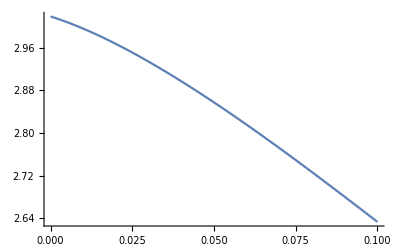
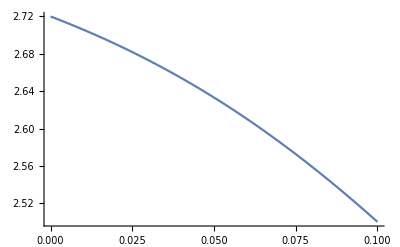
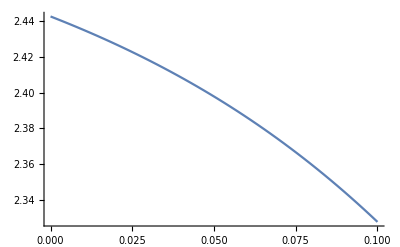

```mathematica
Table[
Plot[-1/λ[[2]]/.sym/.diff/.{koff->0.1,kon->0.1,KKp->0.01,Kp->0.05,κm->y,κp->z},
{y,0.0,0.1}],
{z,0.05,0.16,0.05}]
```

#### Time evolution

```mathematica
(*No way*)
```

#### Work rate in steady state

```mathematica
WdotSS=b(Kp Log[Kp/Km]+κp Log[κp])+c(-Km Log[Kp/Km]+κm Log[κm])+
+bb(-KKm Log[KKp/KKm]+κκm Log[κκm])+cc(KKp Log[KKp/KKm]+κκp Log[κκp])/.SS//Simplify;
WdotSS/.diff/.sym;
```

#### Work to sort

```mathematica
(*Not in general*)
```

#### Intermediate steady state

```mathematica
IntSS=Solve[M[[2;;-2,;;]].x=={0,0,0,0},{b,bb,c,cc}]//Flatten//Simplify;
(*Assume boxes much larger than channel*)
IntSS=IntSS/.{a2->n-a1}//Simplify
```

{b→(kon (Km n+a1 (koff+κm)))/(Km (koff+κp)+(koff+κm) (koff+Kp+κp)),bb→(kon (KKp n+a1 (koff+κκp)))/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp)),c→(kon (-a1 (koff+κp)+n (koff+Kp+κp)))/(Km (koff+κp)+(koff+κm) (koff+Kp+κp)),cc→(kon (-a1 (koff+κκm)+n (KKm+koff+κκm)))/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp))}

#### Evolution of A1 in intermediate SS

```mathematica
a1dotIntSS=M[[1]].x/.IntSS//FullSimplify;
Collect[a1dotIntSS,a1]
(*Evolution is exponential decay to SS*)
a1IntSS=f[t]/.DSolve[f'[t]==(a1dotIntSS/.a1->0)+D[a1dotIntSS,a1]f[t]&&f[0]==n/2,f[t],t];
```

kon ((Km koff n)/(Km (koff+κp)+(koff+κm) (koff+Kp+κp))+(n κm (koff+Kp+κp))/(Km (koff+κp)+(koff+κm) (koff+Kp+κp))+(KKp koff n)/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp))+(n (KKm+koff+κκm) κκp)/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp)))+a1 kon (-2+(koff (koff+κm))/(Km (koff+κp)+(koff+κm) (koff+Kp+κp))-(κm (koff+κp))/(Km (koff+κp)+(koff+κm) (koff+Kp+κp))+((-koff-κκm) κκp)/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp))+(koff (koff+κκp))/(KKm (koff+κκp)+(koff+κκm) (KKp+koff+κκp)))

#### Time-scale in intermediate SS

```mathematica
(*τIntSS=Assuming[kon>0&&koff>0&&Kp>0&&Km>0&&KKp>0&&KKm>0&&κp>0&&κm>0&&κκp>0&&κκm>0,
Limit[a1IntSS,t->∞]]//Simplify*)
τIntSS=-1/D[a1dotIntSS,a1];
```

#### Work to sort assuming intermediate SS

```mathematica
Wt=b(Kp Log[Kp/Km]+κp Log[κp])+c(-Km Log[Kp/Km]+κm Log[κm])+
+bb(-KKm Log[KKp/KKm]+κκm Log[κκm])+cc(KKp Log[KKp/KKm]+κκp Log[κκp])/.IntSS;
Wt=Wt/.a1->a1IntSS//Simplify;
WtotIntSS=Integrate[Wt,{t,0,τIntSS}]//Simplify;
```

#### Plots

```mathematica
(*Define entropy*)
S[a1_]:=(a1 Log[a1]+(1-a1)Log[1-a1])/Log[2]
```

Distribution of ΔS

```mathematica
ki=0.005;
kf=0.021;
dk=0.002;
(*diff and sym*)
klist=Table[{kon->vkon,koff->vkoff,Kp->vKp,KKp->vKKp,κp->vκp,κm->vκm},
{vkon,ki,kf,dk},
{vkoff,ki,kf,dk},
{vKp,ki,kf,dk},
{vKKp,ki,kf,dk},
{vκp,ki,kf,dk},
{vκm,ki,kf,dk}];
klist=Flatten[klist,5];
klist//Length
(*Eliminate where Kp<KKpm and where κp<κm*)
Position[{KKp≤Kp}/.klist//Flatten,_?(#==True&)]//Flatten;
klist=klist[[%]];
Position[{κm≤κp}/.klist//Flatten,_?(#==True&)]//Flatten;
klist=klist[[%]];
klist//Length
```

```mathematica
a1list=(a1/n)/.SS/.diff/.sym/.klist//Flatten;
Slist=S[a1list];
τlist=τIntSS/.diff/.sym/.klist//Flatten;
Wlist=WtotIntSS/n/.diff/.sym/.klist//Flatten;
```

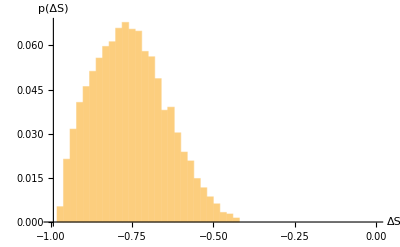

```mathematica
Histogram[Slist,Automatic,"Probability",
PlotRange->{{-1,0},Automatic},
AxesLabel->{Style["ΔS",FontSize->16],Style["p(ΔS)",FontSize->16]}]
```

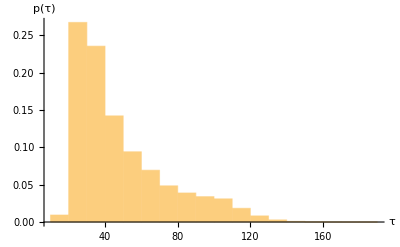

```mathematica
Histogram[τlist,Automatic,"Probability",
PlotRange->Automatic,
AxesLabel->{Style["τ",FontSize->16],Style["p(τ)",FontSize->16]}]
```

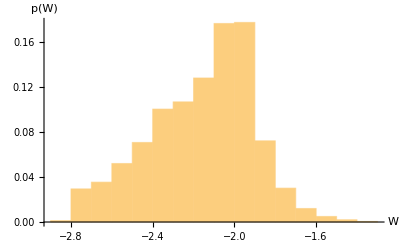

```mathematica
Histogram[Wlist,Automatic,"Probability",
PlotRange->Automatic,
AxesLabel->{Style["W",FontSize->16],Style["p(W)",FontSize->16]}]
```

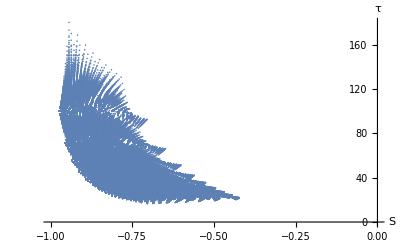

```mathematica
ListPlot[{Slist,τlist}//Transpose,
PlotRange->{{-1,0},Automatic},
AxesLabel->{Style["S",FontSize->16],Style["τ",FontSize->16]}]
```

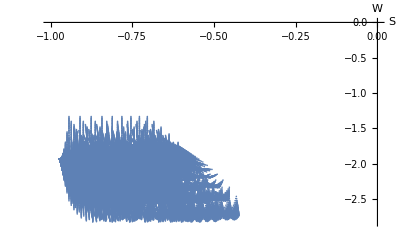

```mathematica
ListPlot[{Slist,Wlist//Flatten}//Transpose,
PlotRange->{{-1,0},Automatic},
AxesLabel->{Style["S",FontSize->16],Style["W",FontSize->16]}]
```

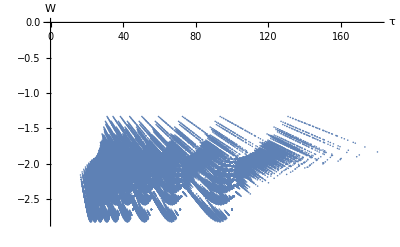

```mathematica
ListPlot[{τlist,Wlist}//Transpose,
PlotRange->Automatic,
AxesLabel->{Style["τ",FontSize->16],Style["W",FontSize->16]}]
```

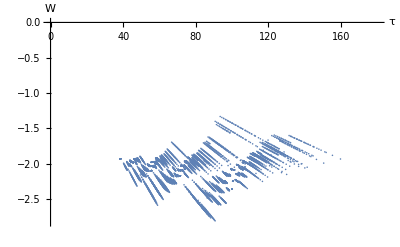
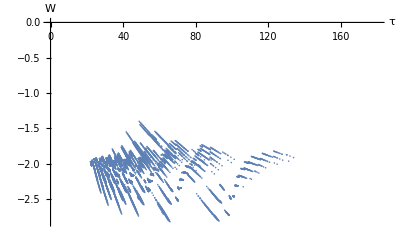
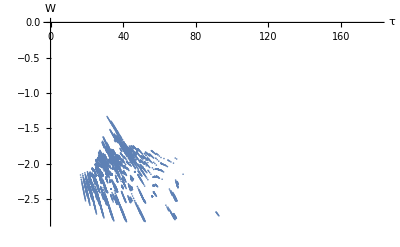
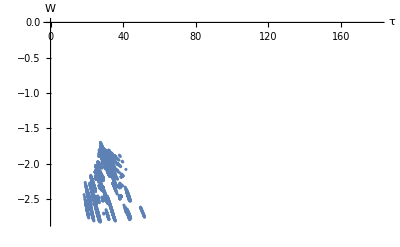
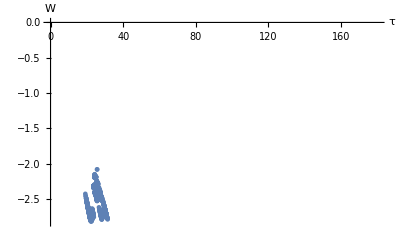
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dS=0.01;
nchunk=10;
Table[
ListPlot[
{τlist[[Flatten[Position[Slist,_?(Sav-dS≤#≤Sav+dS &)]]]],Wlist[[Flatten[Position[Slist,_?(Sav-dS≤#≤Sav+dS &)]]]]}//Transpose,
PlotRange->{{0,Max[τlist]},{Min[Wlist],0}},
AxesLabel->{Style["τ",FontSize->16],Style["W",FontSize->16]}
],
{Sav,-1.0,-0.4,1/nchunk}]
```

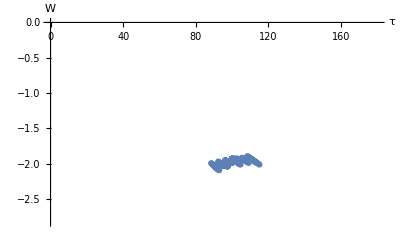

```mathematica
dS=0.005;
nchunk=10;
Sav=-0.97;
idx=Flatten[Position[Slist,_?(Sav-dS≤#≤Sav+dS &)]];
ListPlot[
{τlist[[idx]],Wlist[[idx]]}//Transpose,
PlotRange->{{0,Max[τlist]},{Min[Wlist],0}},
AxesLabel->{Style["τ",FontSize->16],Style["W",FontSize->16]}
]
```